# Open 8 channels Test 7 dat file and show its data..for Read to work, the data should be space separated

/home/pi/2016_6_25_28.dat

```mathematica
datafile = SystemDialogInput["FileOpen"]
```

/home/pi/2016_6_25_28.dat

```mathematica
descriptionfile = datafile<>".txt"
```

/home/pi/2016_6_25_28.dat.txt

```mathematica
description = Import[descriptionfile,"List"]
```

{1466861802,255724,1466867826,498879,11660}

```mathematica
dataseconds = description[[3]]-description[[1]]
```

6024

```mathematica
datausecs = description[[4]]-description[[2]]
```

243155

```mathematica
npoints=description[[5]]
```

11660

```mathematica
frametime = (dataseconds*1.0*^6+datausecs)/npoints
```

516659.

```mathematica
data = Import[datafile];
```

```mathematica
plotdata = Transpose[data];
```

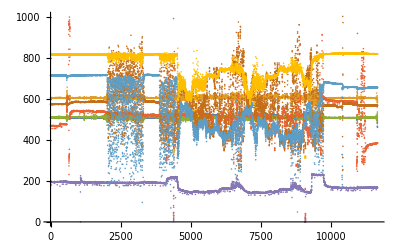

```mathematica
ListPlot[plotdata]
```

```mathematica
Manipulate[
ListPlot[plotdata, PlotRange->{{ts,te},{low, high}},AxesOrigin->{ts,low},GridLines->Automatic,Joined->True],
{ts,0,npoints,npoints/100},{{te,npoints},ts,npoints,npoints/100},{low,0,1024,100},{{high,1024},low,1024,100}]
```

AoA gain reduction by 3, and Beta reduction by 5, for wedge install,

mustard = az, Green = ay, dark blue = ax,
red = rudder, purple = elevator, brown = Beta
light blue = Alpha, yellow = Vrel

```mathematica
Take[data,{1,10}]
```

{{508,605,510,468,193,575,714,817},{508,606,511,468,194,574,715,817},{508,605,510,468,194,573,715,818},{507,605,509,467,194,574,715,816},{507,605,509,468,193,575,714,817},{508,605,510,467,194,573,713,817},{507,605,511,469,194,571,714,817},{508,605,509,455,194,574,714,817},{508,605,510,465,193,572,714,816},{508,605,510,468,193,574,714,816}}